# Optimal Racing Line

## 2D, One Tire

Longitudinal Pajecka

```mathematica
ClearAll[b];
b[symbolic]={b0,b1/MN,b2/K,b3/MN,b4/K,b5/KN,b6/KN^2,b7/KN,b8,b9/KN,b10};
b[ferrari]={b0->1.65,b1->0.,b2->1688.,b3->0.,b4->229,b5->0.,b6->0.,b7->0.,b8->-10.,b9->0.,b10->0.};
b[n_Integer]:=b[symbolic][[n+1]];
ClearAll[muPeak,bigD,bb0d,bigB];
muPeak[fz_]:=b[1]fz+b[2];
bigD[fz_]:=muPeak[fz]fz;
bb0d[fz_]:=(b[3] fz^2+b[4]fz)ⅇ^(-b[5]fz);
bigB[fz_]:=bb0d[fz]/(b[0]bigD[fz]);
ClearAll[numRulez];
numRulez={MN->Mega Newton,KN->Kilo Newton,N->Newton,K->1000.,Kilo->1000.,Mega->1000000,0.->0,1.->1,-1.->1,100.->100,Deg->1};
ClearAll[bigS,bigE,fx,fz,fxNum];
bigS[σ_,fz_]:=(100σ)+b[9]fz+b[10];
bigE[fz_]:=b[6] fz^2+b[7]fz+b[8];
fx[σ_,fz_]:=Module[{SB=bigS[σ,fz]bigB[fz],e=bigE[fz]},
bigD[fz]Sin[b[0] ArcTan[SB+e(ArcTan[SB]-SB)]]];
fxNum[σ_,fz_:3300Newton]:=fx[σ,fz]/Newton/.b[ferrari]/.numRulez;
```

```mathematica
Plot3D[fxNum[σ,fz Newton],{σ,-.20,.20},{fz,1,5000},ViewPoint->{-1.3,2.4,1.5}]
```

-Graphics3D-

Lateral Pajecka

```mathematica
ClearAll[a];
a[symbolic]={a0,a1/MN,a2/K,a3 N/Deg,a4 KN,a5/Deg,a6/KN,a7,a8,a9 Deg/KN,a10 Deg,a111/(MN Deg),a112/(K Deg),a12/K,a13 N};
a[ferrari]={a0->1.799,a1->0.,a2->1688.,a3->4140.,a4->6.026,a5->0.,a6->-0.3589,a7->1.,a8->0.,a9->0.(*-6.111/1000.*),a10->0.(*-3.224/100.*),a111->0.,a112->0.,a12->0.,a13->0.};
a[n_Integer]:=a[symbolic][[n+1]];
ClearAll[muyPeak,bigDy,ba0dy,bigBy];
muyPeak[fz_]:=a[1]fz+a[2];
bigDy[fz_]:=muyPeak[fz]fz;
ba0dy[fz_,γ_:0.]:=a[3]Sin[2ArcTan[fz/a[4]]](1-a[5]Abs[γ]);
bigBy[fz_,γ_:0.]:=ba0dy[fz,γ]/(a[0]bigDy[fz]);
ClearAll[bigSy,bigSyv,bigEy,fy,fz,fyNum];
bigSy[α_,fz_,γ_:0.]:=α+a[8]γ+a[9]fz+a[10];
bigSyv[fz_,γ_:0.]:=((a[11]fz+a[12])γ+a[13])fz+a[14];
bigEy[fz_]:=a[6]fz+a[7];
fy[α_,fz_,γ_:0.]:=Module[{SB=bigSy[α,fz,γ]bigBy[fz,γ],e=bigEy[fz]},
bigDy[fz]Sin[a[0] ArcTan[SB+e(ArcTan[SB]-SB)]]];
fyNum[α_,fz_:3300Newton,γ_:0.]:=fy[α,fz,γ]/Newton/.a[ferrari]//.numRulez;
```

```mathematica
Plot3D[fyNum[α,fz Newton],{α,-20,20},{fz,1,5000},ViewPoint->{-1.3,2.4,1.5},PlotPoints->25]
```

-Graphics3D-

Combination Slip

```mathematica
ClearAll[vHubEarth,wContactHub,lContactEarth,ωHub,effectiveRadius,longSlip,latSlip];
longSlip[ω_,re_,v3_,w3_]:=With[{v=Norm[v3]},
Piecewise[{{(-v3⟦1⟧-w3⟦1⟧)/v, v≠0}, {0, True}}]];
latSlip[v3_,w3_]:=ArcTan[v3⟦1⟧,v3⟦2⟧+w3⟦2⟧];
```

Combination Grip

```mathematica
fxNum[σ]
```

5570.4 Sin[1.65 ArcTan[8.22203 σ-10. (-8.22203 σ+ArcTan[8.22203 σ])]]

```mathematica
fyNum[α]
```

5570.4 Sin[1.799 ArcTan[0.348088 α-0.18437 (-0.348088 α+ArcTan[0.348088 α])]]

```mathematica
UnitConvert[Quantity[3300.,"Newton"],"PoundsForce"]
```

741.87 lbf

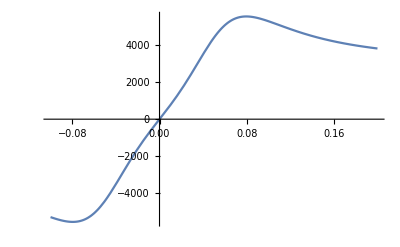

```mathematica
Plot[fxNum[σ],{σ,-0.1,0.2}]
```

```mathematica
FindMaximum[fxNum[σ],σ]
```

{5570.4,{σ→0.079607}}

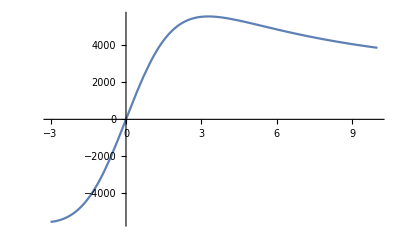

```mathematica
Plot[fyNum[α],{α,-3,10}]
```

```mathematica
FindMaximum[fyNum[α],α]
```

{5570.4,{α→3.27398}}

Magic Trick